```mathematica
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[1,2,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};
σ[1,2,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}/3;
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];
ΩR=3;
θ=0Pi/2;
r[5]=1 λ0;
r[4]=0.5λ0;
r[3]=0.5λ0;
r[2]=0.λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[1,1]=1;
γ[2,2]=1;
γ[1,2]=γ[2,1]=0;
γp[1,1]=1;
γp[2,2]=1;
γp[1,2]=γp[2,1]=0;

V=0.5ΩR Sum[Exp[-I θ]Exp[-I k0 r[i]]σ[1,i,0]+Exp[I θ]Exp[I k0 r[i]]σ[1,i,1],{i,1,2}];
SQ=-0.5sh ch Sum[γp[i,j](Cos[k0 r[α]]Cos[k0 r[3-α]]ρ[t].σ[i,α,β].σ[i,-α+3,β]+Cos[k0 r[α]]Cos[k0 r[3-α]]σ[i,α,β].σ[j,-α+3,β].ρ[t]-2Cos[k0 r[α]]Cos[k0 r[3-α]]σ[j,α,β].ρ[t].σ[i,-α+3,β]),{i,1,atom},{j,1,atom},{α,1,2},{β,0,1}]-0.5(sh^2+1)Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,1].σ[j,α,0]+Cos[k0 r[α]]^2σ[i,α,1].σ[j,α,0].ρ[t]-2Cos[k0 r[α]]^2σ[j,α,0].ρ[t].σ[i,α,1]),{i,1,atom},{j,1,atom},{α,1,2}]-0.5 sh^2Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,0].σ[j,α,1]+Cos[k0 r[α]]^2σ[i,α,0].σ[j,α,1].ρ[t]-2 Cos[k0 r[α]]^2σ[j,α,1].ρ[t].σ[i,α,0]),{i,1,atom},{j,1,atom},{α,1,2}]-I Sum[Λ[i,j](Cos[k0 r[α]]Cos[k0 r[α]]σ[i,α,1].σ[j,α,0].ρ[t]-Cos[k0 r[α]]Cos[k0 r[α]]ρ[t].σ[i,α,1].σ[j,α,0]),{i,1,atom},{j,1,atom},{α,1,2}];

DR=-I (V.ρ[t]-ρ[t].V);
solsq=NDSolve[{ρ'[t]==SQ+DR,ρ[0]==init},slnn,{t,0,1000}];
```

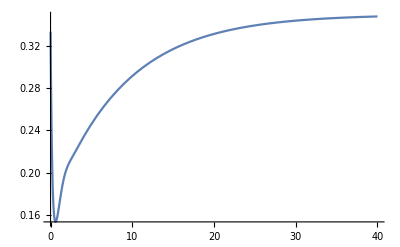

```mathematica
Plot[a[1,1][t]/.solsq,{t,0,40},PlotRange->All]
```

```mathematica
ρ[t]/.solsq/.t->1000//MatrixForm
```

((0.349502+7.24482×10^-20 ⅈ
1.03014×10^-20-0.0496959 ⅈ
-0.251614-5.2157×10^-20 ⅈ) | (-1.03014×10^-20+0.0496959 ⅈ
0.164236+3.40445×10^-20 ⅈ
1.21453×10^-20-0.0585912 ⅈ) | (-0.251614-5.2157×10^-20 ⅈ
-1.21453×10^-20+0.0585912 ⅈ
0.486261+1.00797×10^-19 ⅈ))

```mathematica
ρ[t]/.solsq/.t->1000//MatrixForm
```

((0.367099
4.19898×10^-53
-0.482014) | (4.19898×10^-53
5.40893×10^-16
-5.51341×10^-53) | (-0.482014
-5.51341×10^-53
0.632901))

```mathematica
ρ[t]/.solsq/.t->1000//MatrixForm
```

((0.114318+1.3322×10^-25 ⅈ
-1.02167×10^-13-0.0739241 ⅈ
-0.0593114-4.46149×10^-12 ⅈ) | (-1.02167×10^-13+0.0739241 ⅈ
0.263074+3.05614×10^-25 ⅈ
2.82351×10^-12-0.165446 ⅈ) | (-0.0593114+4.46149×10^-12 ⅈ
2.82351×10^-12+0.165446 ⅈ
0.622608+7.31701×10^-25 ⅈ))

```mathematica
ρ[t]/.solsq/.t->1000//MatrixForm
```

((0.114318+1.3322×10^-25 ⅈ
-1.02167×10^-13-0.0739241 ⅈ
-0.0593114-4.46149×10^-12 ⅈ) | (-1.02167×10^-13+0.0739241 ⅈ
0.263074+3.05614×10^-25 ⅈ
2.82351×10^-12-0.165446 ⅈ) | (-0.0593114+4.46149×10^-12 ⅈ
2.82351×10^-12+0.165446 ⅈ
0.622608+7.31701×10^-25 ⅈ))